```mathematica
SetDirectory[NotebookDirectory[]];
```

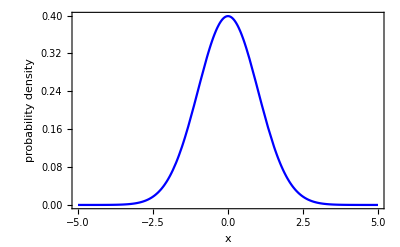

```mathematica
g=Plot[PDF[NormalDistribution[0,1],x],{x,-5,5},Axes->None,Frame->{True,True,False,False},PlotStyle->Blue,FrameTicks->None,FrameLabel->{"x","probability density"},LabelStyle->{Black,FontSize->18}]
```

```mathematica
Export["normal_distribution.pdf",g]
```

normal_distribution.pdf